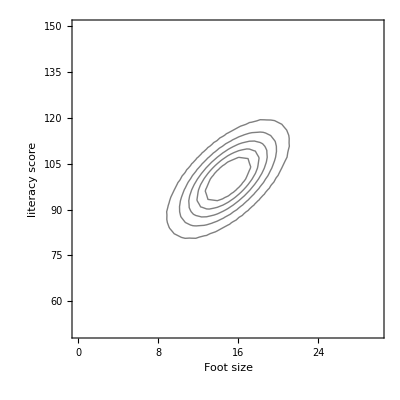

```mathematica
aMultiNormalPDF[x_,y_]:=PDF[MultinormalDistribution[{15,100},{{10,20},{20,100}}],{x,y}]
a1=Show[Plot3D[aMultiNormalPDF[x,y],{x,0,30},{y,50,150},PlotRange->Full,ViewPoint->{-1.0247702550719293,-2.1545047299507063,2.399573981551678},ViewVertical->{0.,0.,1.},BaseStyle->{FontSize->16},AxesLabel->{"Foot size","literacy score","pdf"},Ticks->{True,True,None},ColorFunction->"PigeonTones"],ImageSize->Large];
a2=ContourPlot[aMultiNormalPDF[x,y],{x,0,30},{y,50,150},Contours->{0.001,0.002,0.003,0.004,0.005},PlotRange->Full,Mesh->None,ContourShading->{White},ContourStyle->{Black},FrameLabel->{"Foot size","literacy score"},BaseStyle->{FontSize->16}];
gFinal=Show[GraphicsRow[{a1,a2}],ImageSize->Large]
```

```mathematica
Export["Probability_footSizeIntelligenceTwoDimensionalExample.pdf",gFinal]
```

Probability_footSizeIntelligenceTwoDimensionalExample.pdf